# 2nd Order Σ (p, τ) for BEC Polaron

## Parameters and Equations

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
μ= -790;
```

## Integrating τ1 , τ2 and τ3

```mathematica
Integrand[q1_,q2_,τ_,τ1_, τ2_,costheta_] := 1/(2*Pi)^6*vq2[q1]*vq2[q2]*dq[q1,0,τ]* dq[q2,τ1,τ2]*g0[q1,0,τ1]*g0[q1,τ2,τ]*g0cos[q1,q2,τ1,τ2, costheta];
```

### Plot of final Integrand for q Integral

```mathematica
f[q1_,q2_,τ_,τ2_, costheta_]:=Integrate[Integrand[q1,q2,τ,τ1,τ2, costheta],  {τ1,0,τ2}];
g[q1_,q2_,τ_, costheta_]:=Integrate[f[q1,q2,τ,τ2, costheta],{τ2,0,τ}];
```

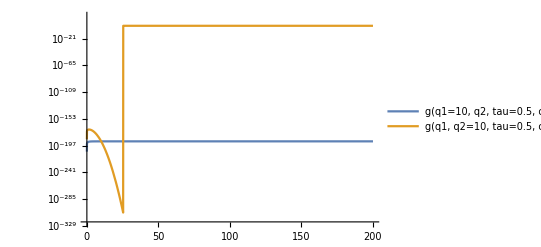

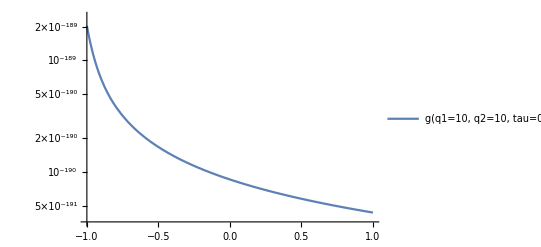

```mathematica
gplot1=LogPlot[{4*Pi*10^2*2*Pi*q^2*g[10,q,0.5, 0],4*Pi*q^2*2*Pi*10^2* g[q,10,0.5,0]},{q,0,qc}, PlotLegends -> {"g(q1=10, q2, tau=0.5, costheta=0)", "g(q1, q2=10, tau=0.5, costheta=0)"}]
gplot2 =LogPlot[4*Pi*10^2*2*Pi*10^2*g[10,10,0.5, t],{t,-1,1}, PlotLegends -> {"g(q1=10, q2=10, tau=0.5, costheta)"}]
```

## Q Integral

### Q2 Integral in sphere coordinates with theta Integral

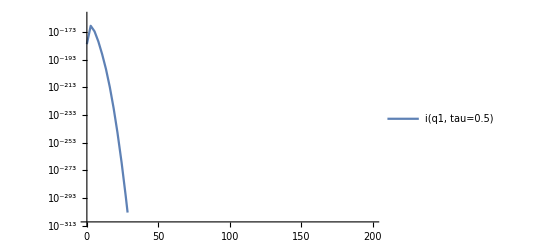

```mathematica
i[q1_,τ_]:=NIntegrate[2*Pi*q2^2*g[q1,q2,τ, costheta],{costheta,-1,1},{q2,0,qc} ];
iplot=LogPlot[4*Pi*q^2*i[q,0.5],{q,0,qc},  PlotPoints->10, MaxRecursion->3, PlotRange->Full,PlotLegends -> {"i(q1, tau=0.5)"}]
```

### Q1 Integral in sphere coordinates

```mathematica
se[τ_]:=NIntegrate[4*Pi*q1^2*2*Pi*q2^2*g[q1,q2,τ, costheta],{q1,0,qc},{costheta,-1,1},{q2,0,qc} ];
```

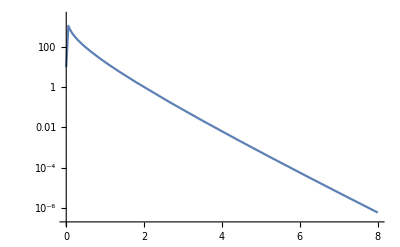

```mathematica
LogPlot[se[τ],{τ,0,8}, PlotPoints->10, MaxRecursion->4, PlotRange->Full, PlotLegends->"Se"]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

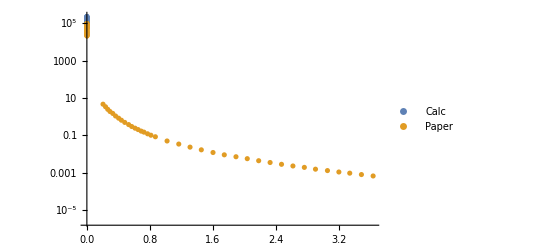

```mathematica
data = Table[{τ, se[τ]*Exp[μ*τ]},{τ, 0, 8*10^-4, 2.5*10^-5}];
ListLogPlot[{data, paper},PlotLegends->{"Calc", "Paper"} ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

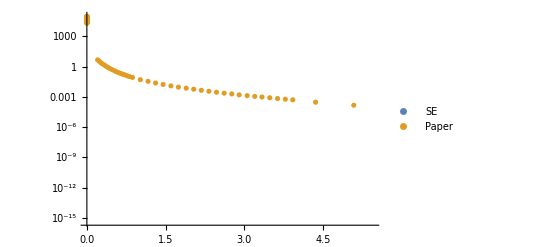

```mathematica
data2 = Table[{τ, se[τ]},{τ, 0.1, 8, 0.2}];
ListLogPlot[{data2, paper},PlotLegends->{"SE", "Paper"} ]
```

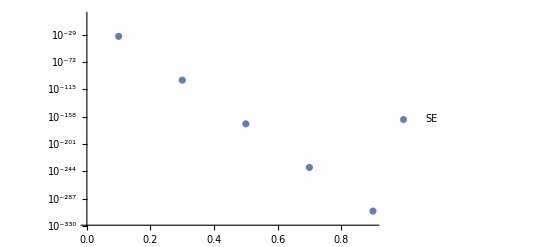

```mathematica
ListLogPlot[data2,PlotLegends->{"SE", "Paper"} ]
```

```mathematica
DumpSave["2nd_G0SE.mx", {iplot, hplot1,hplot2, data}];
Export["mat_2nd_se", data, "Table"];
Export["mat_2nd_seexpmutau", data2, "Table"];
```

## Laplace Transform to Σ2 (p=0, ω)

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/BEC"];
<<2nd_SEw.mx;
```

```mathematica
LaplaceData = Table[{ω,NIntegrate[4*Pi*q1^2*2*Pi*q2^2*g[q1,q2,τ, costheta]* Exp[ω*τ],{q1,0,qc},{costheta,-1,1},{q2,0,qc} ,{τ,0,Infinity}]},{ω,-100,-1, 5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 129.146 and 0.000130387 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 168.998 and 0.000195756 for the integral and error estimates.

{{-100,39.8517},{-95,41.1324},{-90,42.5173},{-85,39.7773},{-80,41.4063},{-75,43.1935},{-70,45.1656},{-65,47.3562},{-60,49.8078},{-55,52.5757},{-50,55.7326},{-45,59.3775},{-40,63.6481},{-35,68.7435},{-30,74.9642},{-25,82.7906},{-20,93.0493},{-15,107.32},{-10,129.146},{-5,168.998}}

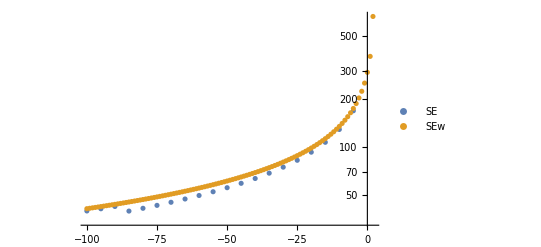

```mathematica
ListLogPlot[{LaplaceData, Σ2omegadata}, PlotLegends -> {"SE", "SEw"}]
```